```mathematica
Author: Daniel von Rauchhaupt

SIRVD-Model

Relevant parameters for the simulation are:
	1. Total initial population (initPop)
	2. Total number of infected people (initInf) during initialization (Healthy people = initPop-initInf).
	3. Exposure rate (β).
	4. Recovery rate (γ).
			The recovery rate is equal to 1/n, with n being the average duration of the disease.
	5. Transition rate (τ) from status recovered back to susceptible of any given individual per iteration.
			Again, the transition rate can also be denoted as 1/n, with n being the average duration an individual remains
			immune to the disease after having recovered from the disease previously.
	6. Vaccination rate (ϕ).
	7. Mortality rate (μ).
	8. Number of iterations (iterations) during the simulation.
```

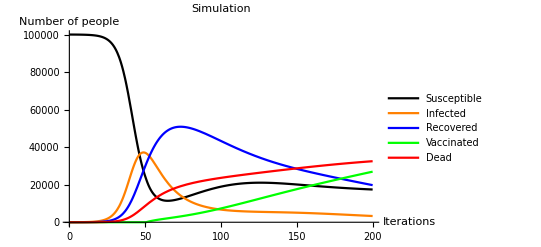

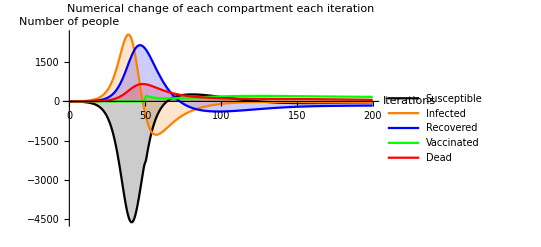

```mathematica
(*Clearing all variables*)
Clear["Global`*"];

(*Starting parameters. Edit here to change the outcome of the simulation*)
initPop=100000;
initInf=10;
β=exposureRate=0.3;
γ=recoveryRate=1/14;
τ=transRate=1/50; 
ϕ=vacinationRate=1/100;
μ=mortalityRate=1/56;
startVac=50;
iterations=200;

(*Defining the neccessary differential equations according to the theory presented in the paper*)
totalPop=s[t]+i[t]+v[t]+r[t];
eqS=s'[t]==-(β i[t] s[t])/totalPop-ϕ s[t] Min[1,Max[0,t-startVac]]+τ r[t];
eqI=i'[t]==(β i[t] s[t])/totalPop-γ i[t]-μ i[t];
eqR=r'[t]==γ i[t]-τ r[t];
eqV=v'[t]==ϕ s[t] Min[1,Max[0,t-startVac]];
eqD=d'[t]==μ i[t];

(*Solving the differential equation system with the given start parameters*)
sol=NDSolve[{
(*Defining the functions that should be solved*)
eqS,
eqI,
eqR,
eqV,
eqD,

(*Defining proper starting values*)
(*Number of susceptible people during initialization is the total population without the initial number of infected individuals*)
s[0]==1. initPop-initInf,
i[0]==1. initInf,
r[0]==0.,
v[0]==0.,
d[0]==0.
(*Starting values are initialized as floats. The Hardware is usually more efficient when working with floats*)
},
{s,i,r,v,d},
{t,iterations}];

(*Parsing the solutions of the differential equation system into more easily usable forms*)
solS=First[s/.sol];
solI=First[i/.sol];
solR=First[r/.sol];
solV=First[v/.sol];
solD=First[d/.sol];

(*Plotting the simulation*)
Plot[{solS[t],solI[t],solR[t],solV[t],solD[t]},{t,0,iterations},
PlotStyle->{Black,Orange,Blue,Green,Red},
PlotRange->Automatic,
Filling->None,
AxesLabel->{"Iterations","Number of people"},
PlotLabel->"Simulation",
PlotLegends->{"Susceptible","Infected","Recovered","Vaccinated","Dead"}
]

(*Plotting the numerical change of each compartment each iteration*)
Plot[{solS[t+1]-solS[t],solI[t+1]-solI[t],solR[t+1]-solR[t],solV[t+1]-solV[t],solD[t+1]-solD[t]},{t,0,iterations},
PlotStyle->{Black,Orange,Blue,Green,Red},
PlotRange->All,
Filling->Axis,
AxesLabel->{"Iterations","Number of people"},
PlotLabel->"Numerical change of each compartment each iteration",
PlotLegends->{"Susceptible","Infected","Recovered","Vaccinated","Dead"}
]
```